# MATH299M/CMSC389W - Visualization through Mathematica Lesson 14: Evaluation Control

This lecture is an introduction and foray into some of the more technical details associated with how Mathematica evaluates expressions. The contents of this notebook aren’t meant to have explicit uses for your notebooks. Rather, they will hopefully find some use as you create more complex models. They are provided to introduce you to their presence in the case that you need them.

## Assignment and Delayed Assignment

Very early on, we saw how to perform assignment in Mathematica.

```mathematica
x=5;x
```

5

It is clear that using the = operator allows us to immediately assign a value to a variable.

```mathematica
y=3;
x=y+4;
y=4;
x
```

7

Furthermore, it is clear that the right hand side (RHS) of the =  operator is evaluated immediately; later changing y to 4 does not affect the value of x.

```mathematica
f[x_]:=x+4;
f[3]
```

7

We also saw how to use the := operator to define functions. The := is called the delayed assignment operator, it the significant distinction between the regular assignment and delayed assignment operator is when the RHS is evaluated. For the assignment (=) operator, it’s immediately; for the delayed assignment operator, it’s on demand. Because there’s no actual need to use delayed assignment with function definitions, we can start doing interesting things like this:

```mathematica
x=.; (* This is the Unset operator; it removes the value associated with x *)
y=3;
f[x_]:=x+4+y;
g[x_]=x+4+y;
y=4;
f[4]
g[4]
```

12

11

When the regular assignment operator is used for g, the RHS immediately evaluates to x+7. For the delayed assignment operator, the RHS remains as x+4+y, so when we change y to 4 after the definition of the functions, we get 12 as opposed to 11. Okay, so why don’t we use regular assignment with function definitions? Observe:

```mathematica
x=7;
f[x_]=2 x;
f[3] (* Should be 6 *)
```

14

Wait a second! What happened? Because the RHS is evaluated immediately, it uses the value of x previously defined instead of the value of x that is passed into the function. That’s why I had to unset x in the previous example. One may ask what happens if we use variable assignment with the delayed assignment operator:

```mathematica
y=3;
x:=y+6;
y=2;
x
```

8

Much like in the function example, we see the RHS of the definition of x evaluate only on demand, thus using the y=2 value instead of y=3.

```mathematica
x=.
```

## Hold and Evaluate

Now we consider the humble expression and its evaluation. You’ve seen both of these before. Every formula, piece of arithmetic, function call, manipulate are all expressions, and Mathematica has special rules for how different kinds and parts of expressions are evaluated. For example, we saw above that we can change when the RHS of an assignment operation is evaluated. We can in fact do the same for any arbitrary expression in any place.

Firstly, the Hold function prevents an expression from being evaluated.

```mathematica
{1+1,Hold[1+1]}
```

{2,Hold[1+1]}

We can release the hold with ReleaseHold

```mathematica
ReleaseHold[{2,Hold[1+1]}]
```

{2,2}

When we use variable assignment, we’re actually using the Hold function. Variable assignment with = and delayed assignment with := actually correspond to two functions: Set and SetDelayed

```mathematica
Set[x, 2];
x
SetDelayed[y, x];
Set[x, 3];
y
```

2

3

```mathematica
x=.; y=.; (* Clean up variables *)
```

The first argument of both Set and SetDelayed are “held” in order to allow assignment to occur. If we were to perform Set[x, 2] and then Set[x, 3] and the first argument wasn’t held, then Set would be trying to assign the value 3 to 2 (which doesn’t make any sense). This behavior prevents things like the following from working:

```mathematica
3x-2x=3;
```

Set::write: Tag Plus in -2 x+3 x is Protected.

The error message reports that I can’t assign a value to an algebraic expression. Equivalently,

```mathematica
Set[3x-2x,3];
```

Set::write: Tag Plus in -2 x+3 x is Protected.

Now, what if I wanted 3x-2x to evaluate to x and then assign 3 to it? I can use the Evaluate function.

```mathematica
Set[Evaluate[3x-2x],3];
x
```

3

Frankly, this is absurd and a terrifying way to write a notebook. I haven’t a clue why you would do this. Notice, if I try to do this trick again, when I call Evaluate on the expression, it evaluates to a number. I can’t assign a number to another number, so it again fails.

```mathematica
Set[Evaluate[3x-2x],5];
```

Set::setraw: Cannot assign to raw object 3.

Normally, Set (or the = operator) wraps the first argument (or the LHS of the =) in Hold. This allows us to repeatedly reassign a value to a variable as the Hold prevents the first argument (or LHS) from reevaluating into some previous value (and thus preventing the “Cannot assign to raw object” error). We’ve circumvented this by nesting Evaluate inside of Hold, asking Mathematica to first evaluate the expression in the first argument (or LHS) before holding it and assigning a value to it. 

Regardless of how odd and edge casey this may be, I’m using it as a vessel to make a point here: Mathematica will really let you do a lot of stupid stuff, and that includes messing with what it thinks is right. For Plot to work correctly, Mathematica uses Hold on its arguments. If I first assign a value to x and then Plot a function over x, then Plot graphs the function and not the function evaluated at x.



```mathematica
x=5;
Plot[Sin[x],{x,0,2π}]
```

This is great and means when we can interchange variables we plot over and variables that we might want to use as constants.

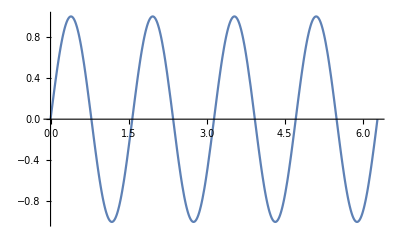

```mathematica
x=123456789342091748912;
k=4;
Plot[Sin[k x],{x,0,2π}]
```

```mathematica
x=.; (* Clean up variables *)
```

Internally, Plot Holds the first argument. It then replaces every instance of x, the variable being plotted over, with a sampled value on x_min to x_max. It then evaluates that expression. The replacement following the Hold is crucial; it prevents the x from the outside from interfering with the plot. However, there are issues that arise:

```mathematica
Plot[D[Sin[x],x],{x,0,2π}]
```

General::ivar: 0.000128356 is not a valid variable.

General::ivar: 0.128357 is not a valid variable.

General::ivar: 0.256585 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

Why doesn’t this work? Well, following the explanation from before, Plot Holds the first argument. It then replaces every instance of x with a sampled value on x_min to x_max. Let’s say that value is 1. Then we have, D[Sin[1], 1]. Finally, plot evaluates that. Wait a second, what does it mean to take the derivative with respect to 1!? 1 isn’t a valid variable, hence the errors we see. Previously, we’ve circumvented this by performing a derivative w.r.t. one variable, replacing every instance of that with another, and then plotting over that:

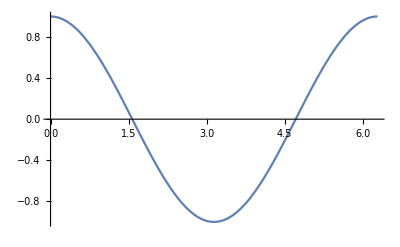

```mathematica
Plot[D[Sin[y],y]/.y->x,{x,0,2π}]
```

This has the problem of being rather cumbersome since we have to keep track of multiple variables. However, we can use Evaluate to achieve the same effect:

```mathematica
Plot[Evaluate[D[Sin[x],x]],{x,0,2π}]
```

-Graphics-

Let’s go through what’s going on here one last time. Evaluate runs on D[Sin[x], x] and evaluates to Cos[x], circumventing Plot’s Hold on the first argument. Plot then replaces every instance of x with values sampled on x_min to x_max. It evaluates that and we get a successful plot!

## Dan Zou - Department of Computer Science MATH299M/CMSC389W Spring 2020 May 1, 2020

## Vlad Dobrin - University of Maryland Computer Science MATH299M/CMSC389W Spring 2020 May 29th, 2020